# A package for the Wright omega function ω(z)

J. M., version of 11/2019

## Introduction

Wright is a Mathematica package that implements the Wright omega function ω(z), a function that is related to the Lambert W function (ProductLog).

Load the package:

```mathematica
<<Wright`
```

Usage message:

```mathematica
??WrightOmega
```

RowBox[{"WrightOmega", "[", StyleBox["z", "TI"], "]"}] is the Wright omega function RowBox[{"ω", "(", StyleBox["z", "TI"], ")"}].

Attributes[WrightOmega]={Listable,NumericFunction,Protected,ReadProtected}
 
SyntaxInformation[WrightOmega]={ArgumentsPattern→{_}}

## Basic Examples

Evaluate at machine precision:

```mathematica
WrightOmega[3.]
```

2.20794

Evaluate at arbitrary precision:

```mathematica
N[WrightOmega[3],100]
```

2.207940031569322998581604122114577938134077806829902117091949440206372627891448454267184991267616459

Evaluate for complex arguments:

```mathematica
N[WrightOmega[5+7I],20]
```

3.101421646096258478+5.9123134436156785654 ⅈ

Some special values:

```mathematica
WrightOmega[{0,1,E+1}]
```

{ProductLog[1],1,ⅇ}

```mathematica
WrightOmega[{∞,-∞,ComplexInfinity}]
```

{∞,0,ComplexInfinity}

Plot the function:

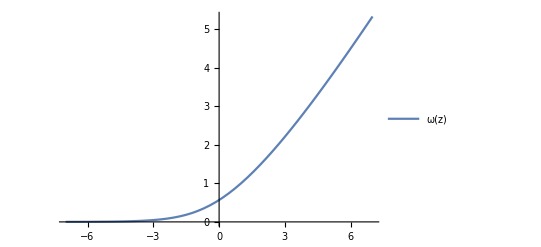

```mathematica
Plot[WrightOmega[z],{z,-7,7},PlotLegends->"AllExpressions"]
```

Plot over the complex plane:

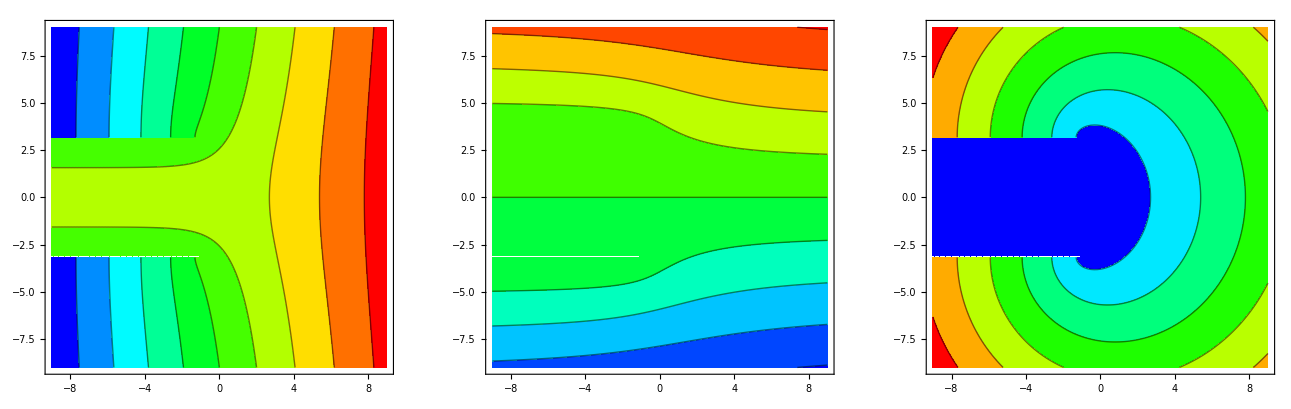

```mathematica
GraphicsRow[{ContourPlot[Re[WrightOmega[x+ⅈ y]],{x,-9,9},{y,-9,9},ColorFunction->(Hue[2 (1-#)/3]&),Exclusions->{{y==π,x<-1},{y==-π,x<-1}},PlotPoints->55],ContourPlot[Im[WrightOmega[x+ⅈ y]],{x,-9,9},{y,-9,9},ColorFunction->(Hue[2 (1-#)/3]&),Exclusions->{{y==π,x<-1},{y==-π,x<-1}},PlotPoints->55],ContourPlot[Abs[WrightOmega[x+ⅈ y]],{x,-9,9},{y,-9,9},ColorFunction->(Hue[2 (1-#)/3]&),Exclusions->{{y==π,x<-1},{y==-π,x<-1}},PlotPoints->55]},ImageSize->Large]
```

```mathematica
GraphicsRow[{Plot3D[Re[WrightOmega[x+ⅈ y]],{x,-9,9},{y,-9,9},Exclusions->{{y==π,x<-1},{y==-π,x<-1}},PlotPoints->45],Plot3D[Im[WrightOmega[x+ⅈ y]],{x,-9,9},{y,-9,9},Exclusions->{{y==π,x<-1},{y==-π,x<-1}},PlotPoints->45],Plot3D[Abs[WrightOmega[x+ⅈ y]],{x,-9,9},{y,-9,9},Exclusions->{{y==π,x<-1},{y==-π,x<-1}},PlotPoints->45]},ImageSize->Large]
```

-Graphics-

Derivatives:

```mathematica
Table[D[WrightOmega[z],{z,k}],{k,5}]
```

{WrightOmega[z]/(1+WrightOmega[z]),-WrightOmega[z]^2/(1+WrightOmega[z])^3+WrightOmega[z]/(1+WrightOmega[z])^2,(3 WrightOmega[z]^3)/(1+WrightOmega[z])^5-(4 WrightOmega[z]^2)/(1+WrightOmega[z])^4+WrightOmega[z]/(1+WrightOmega[z])^3,-(15 WrightOmega[z]^4)/(1+WrightOmega[z])^7+(25 WrightOmega[z]^3)/(1+WrightOmega[z])^6-(11 WrightOmega[z]^2)/(1+WrightOmega[z])^5+WrightOmega[z]/(1+WrightOmega[z])^4,(105 WrightOmega[z]^5)/(1+WrightOmega[z])^9-(210 WrightOmega[z]^4)/(1+WrightOmega[z])^8+(130 WrightOmega[z]^3)/(1+WrightOmega[z])^7-(26 WrightOmega[z]^2)/(1+WrightOmega[z])^6+WrightOmega[z]/(1+WrightOmega[z])^5}

Series expansion:

```mathematica
Series[WrightOmega[z],{z,1,10}]
```

1+(z-1)/2+1/16 (z-1)^2-1/192 (z-1)^3-(z-1)^4/3072+(13 (z-1)^5)/61440-(47 (z-1)^6)/1474560-(73 (z-1)^7)/41287680+(2447 (z-1)^8)/1321205760-(16811 (z-1)^9)/47563407360-(15551 (z-1)^10)/1902536294400+O[z-1]^11

Inverse function:

```mathematica
InverseFunction[WrightOmega][z]
```

z+Log[z]

The package also allows the evaluation of the Lambert W function for arbitrary index, through the identity W_k(z)==ω(log(z)+2 ⅈ π k):

```mathematica
N[ProductLog[3+4ⅈ,2-3ⅈ],20]
```

-27.292491052532934503+15.23427555768828157 ⅈ

```mathematica
D[ProductLog[k,z],{k,4}]
```

-(240 π^4 ProductLog[k,z]^4)/(1+ProductLog[k,z])^7+(400 π^4 ProductLog[k,z]^3)/(1+ProductLog[k,z])^6-(176 π^4 ProductLog[k,z]^2)/(1+ProductLog[k,z])^5+(16 π^4 ProductLog[k,z])/(1+ProductLog[k,z])^4